```mathematica
s = NDSolve[{
f'''[y]-f'[y]f'[y]+f[y]f''[y]==-1,
f[0]==0,
f'[0]==0,
f'[4]== 1.0
},
f,{y,0,4}]
```

{{f→InterpolatingFunction[…]}}

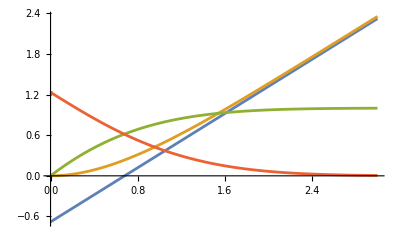

```mathematica
fp=D[f[y]/.s,y];
fpp=D[f[y]/.s,{y,2}];
 Plot[{y-.68,f[y]/.s ,fp,fpp}, {y,0,3}]
```

```mathematica
ψ[x_,y_]:= x f[y]/.s
u[x_,y_]:= x fp
v[x_,y_]:= -f[y]/.s
```

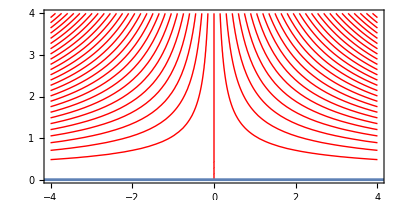

```mathematica
Show[
ContourPlot[ψ[x,y],{x,-4,4},{y,0,4},Contours -> Table[n,{n,-30,30,.5}],ContourShading -> None,ContourStyle -> Red,AspectRatio -> .5],
Plot[0,{x,-5,5}]
]
```

```mathematica
ParametricPlot[{y,2+u[2,y]},{y,0,4}]
```

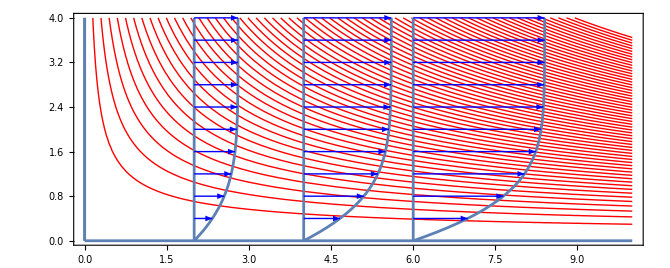

```mathematica
α = 0.4;
Show[
ContourPlot[ψ[x,y],{x,0,10},{y,0,4},Contours -> Table[n,{n,-30,30,.5}],ContourShading -> None,ContourStyle -> {{Red,Thin}},AspectRatio -> .5],
Plot[0,{x,0,10}],
ParametricPlot[
Table[{x,y},{x,0,6,2}],{y,0,4},PlotRange -> All],
ParametricPlot[
Table[{x+α u[x,y][[1]],y},{x,0,6,2}],{y,0,4},PlotRange -> All],
Table[Graphics[{Blue,Arrowheads[0.03],Arrow[{{x,y},{x+α u[x,y][[1]],y}}]}],{y,.4,4,.4},{x,0,6,2}],
AspectRatio -> 0.4
]
```

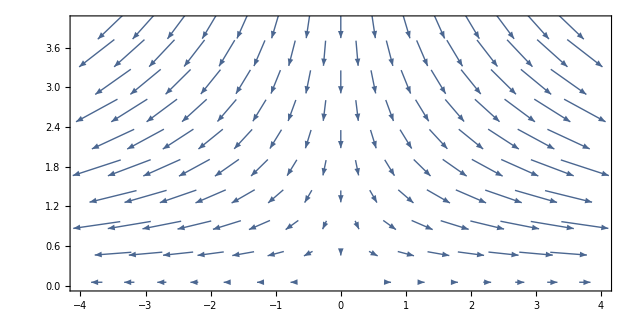

```mathematica
VectorPlot[{u[x,y][[1]],v[x,y][[1]]},{x,-4,4},{y,0,4},AspectRatio -> 0.5,VectorScaling->Automatic,VectorSizes->{0,2},VectorColorFunction -> None]
```

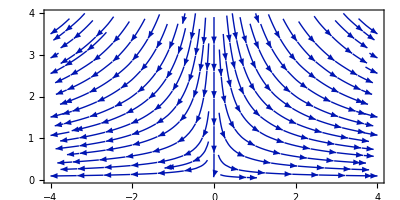

```mathematica
StreamPlot[{u[x,y][[1]],v[x,y][[1]]},{x,-4,4},{y,0,4},AspectRatio -> 0.5]
```